```mathematica
Dt[F[x,y,y']]
```

Dt[y]' F^(0,0,1)[x,y,y']+Dt[y] F^(0,1,0)[x,y,y']+Dt[x] F^(1,0,0)[x,y,y']

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[Dt[f[x]]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
DSolve[{Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==f[x],Dt[Dt[x]]f'[x]==0,Dt[x]^2 f''[x]==f[x]},{f[x]},x]
```

DSolve::overdet: There are fewer dependent variables than equations, so the system is overdetermined.

DSolve[{Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==f[x],Dt[Dt[x]] f'[x]==0,Dt[x]^2 f''[x]==f[x]},{f[x]},x]

```mathematica
Integrate[(√(1+f'[x]^2))^2,x]
```

∫(1+f'[x]^2)ⅆx

```mathematica
With[{f=Function[x, x x]},Integrate[(√(1+f'[x]^2))^2,x]]
```

x+(4 x^3)/3

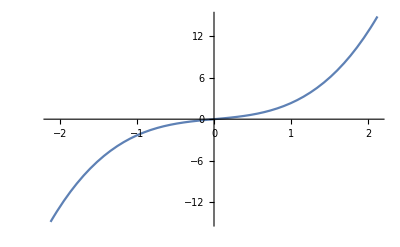

```mathematica
Plot[x+(4 x^3)/3,{x,-2.121320343559643,2.121320343559643}]
```

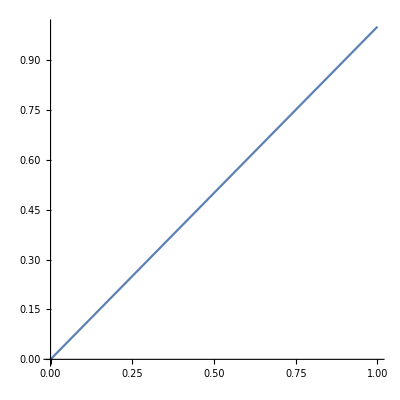

```mathematica
ParametricPlot[
{t,t}
,{t,0,1}]
```

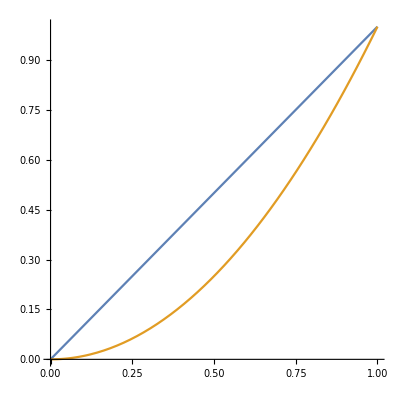

```mathematica
ParametricPlot[{
{t,t},
{t,t^2}
},{t,0,1}]
```

```mathematica
ParametricPlot[{
{t,t},
{t,t^2}
},{t,0,1}]
```

```mathematica
Normalize[{0,f''[t]}].Normalize[{1,f'[t]}]
```

(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])

```mathematica
With[{f=Function[x, x x]},(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])]
```

(2 t)/(√(1+4 Abs[t]^2))

```mathematica
With[{f=Function[x, x x]},FullSimplify[(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]]),Element[t,Reals]]]
```

(2 t)/(√(1+4 t^2))

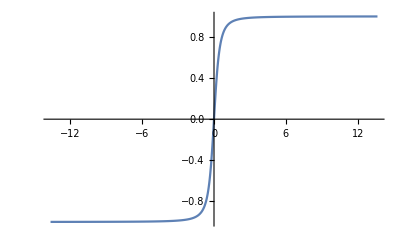

```mathematica
Plot[(2 t)/(√(1+4 t^2)),{t,-13.649999999999999,13.649999999999999}]
```

```mathematica
Tanh[x]
```

Tanh[x]

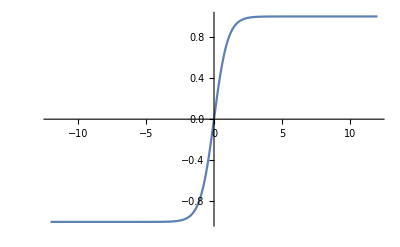

```mathematica
Plot[Tanh[x],{x,-12.,12.}]
```

```mathematica
Normalize@{t,(2 t)/(√(1+4 t^2))}.Normalize@{t,Tanh[t]}
```

t^2/(√(Abs[t]^2+4 Abs[t/(√(1+4 t^2))]^2) √(Abs[t]^2+Abs[Tanh[t]]^2))+(2 t Tanh[t])/(√(1+4 t^2) √(Abs[t]^2+4 Abs[t/(√(1+4 t^2))]^2) √(Abs[t]^2+Abs[Tanh[t]]^2))

```mathematica
With[{f=Function[x, x x]},FullSimplify[Normalize@{t,(2 t)/(√(1+4 t^2))}.Normalize@{t,Tanh[t]},Element[t,Reals]]]
```

(Sign[t] (t √(1+4 t^2)+2 Tanh[t]))/(√((5+4 t^2) (t^2+Tanh[t]^2)))

```mathematica
Plot[(Sign[t] (t √(1+4 t^2)+2 Tanh[t]))/(√((5+4 t^2) (t^2+Tanh[t]^2))),{t,-8,8}]
```

```mathematica
Plot[(Sign[t] (t √(1+4 t^2)+2 Tanh[t]))/(√((5+4 t^2) (t^2+Tanh[t]^2))),{t,-8,8},PlotRange->{.9,1}]
```

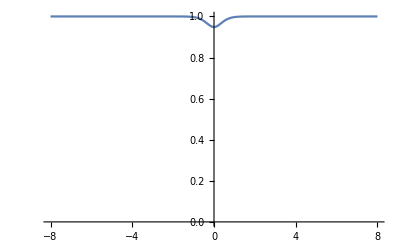

```mathematica
Plot[(Sign[t] (t √(1+4 t^2)+2 Tanh[t]))/(√((5+4 t^2) (t^2+Tanh[t]^2))),{t,-8,8},PlotRange->{0,1}]
```

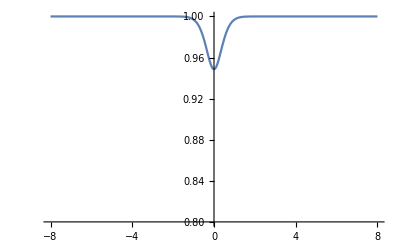

```mathematica
Plot[(Sign[t] (t √(1+4 t^2)+2 Tanh[t]))/(√((5+4 t^2) (t^2+Tanh[t]^2))),{t,-8,8},PlotRange->{.8,1}]
```

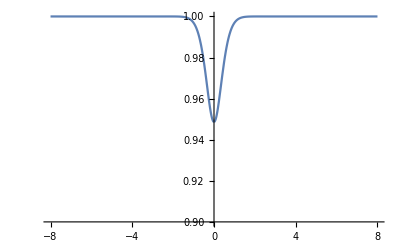

```mathematica
Plot[(Sign[t] (t √(1+4 t^2)+2 Tanh[t]))/(√((5+4 t^2) (t^2+Tanh[t]^2))),{t,-8,8},PlotRange->{.9,1}]
```

```mathematica
Plot[(Sign[t] (t √(1+4 t^2)+2 Tanh[t]))/(√((5+4 t^2) (t^2+Tanh[t]^2))),{t,-8,8},PlotRange->{.9,1}]
```

```mathematica
With[{f=Function[x, x x x+x x+ x]},FullSimplify[(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]]),Element[t,Reals]]]
```

((1+t (2+3 t)) Sign[2+6 t])/(√(1+(1+t (2+3 t))^2))

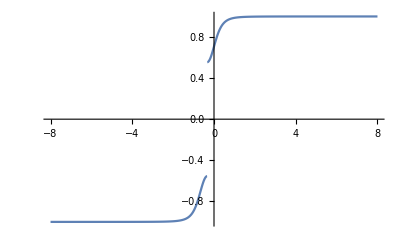

```mathematica
Plot[((1+t (2+3 t)) Sign[2+6 t])/(√(1+(1+t (2+3 t))^2)),{t,-8,8}]
```

```mathematica
With[{f=Function[x, x x]},FullSimplify[(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]]),Element[t,Reals]]]
```

(2 t)/(√(1+4 t^2))

```mathematica
Plot[(2 t)/(√(1+4 t^2)),{t,-13.649999999999999,13.649999999999999}]
```

-Graphics-

```mathematica
FullSimplify[(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])==0,Element[t,Reals]]
```

Sign[f''[t]] f'[t]==0

```mathematica
DSolve[Sign[f''[t]] f'[t]==0,{f[t],f[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[t]→C[1]},{f[t]→C[1]+t C[2]}}

```mathematica
With[{f=Function[x, Sin[x]]},FullSimplify[(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]]),Element[t,Reals]]]
```

-(Cos[t] Sign[Sin[t]])/(√(1+Cos[t]^2))

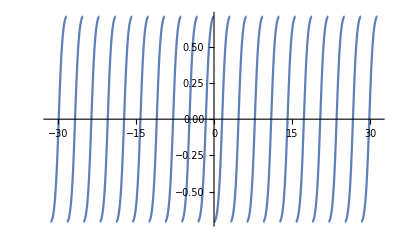

```mathematica
Plot[-(Cos[t] Sign[Sin[t]])/(√(1+Cos[t]^2)),{t,-10 π,10 π}]
```

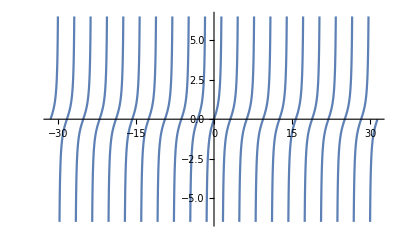

```mathematica
Plot[Tan[t],{t,-10 π,10 π}]
```

```mathematica
Plus[Integers,Integers]->Integers
```

2 ℤ→ℤ

```mathematica
Plus[Rationals,Rationals]->Rationals
```

2 ℚ→ℚ

```mathematica
(1-a)p+a q/.{p->{t,t},q->{t,t t}}
```

{(1-a) t+a t,(1-a) t+a t^2}

```mathematica
ParametricPlot[
{(1-a) t+a t,(1-a) t+a t^2}
,{t,-3,3}]
```

-Graphics-

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a t,(1-a) t+a t^2}
,{t,-3,3}]
,{a,0,1}]
```

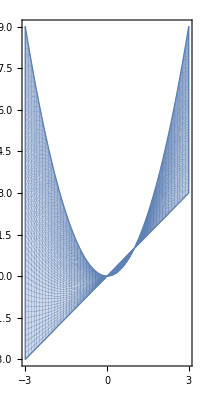

```mathematica
ParametricPlot[
{(1-a) t+a t,(1-a) t+a t^2}
,{t,-3,3},{a,0,1}]
```

```mathematica
Integrate[Integrate[Norm@{(1-a) t+a t,(1-a) t+a t^2},{a,0,1}],{t,-3,3}]
```

$Aborted

```mathematica
{t,t t}-{t, t}
```

{0,-t+t^2}

```mathematica
Norm@{0,-t+t^2}
```

Abs[-t+t^2]

```mathematica
Integrate[Abs[-t+t^2],{t,-3,3}]
```

55/3

```mathematica
N[55/3]
```

18.3333

```mathematica
Norm@Integrate[Integrate[{(1-a) t+a t,(1-a) t+a t^2},{a,0,1}],{t,-3,3}]
```

9

```mathematica
FullSimplify[(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]]),Element[t,Reals]]
```

(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])

```mathematica
FullSimplify[Normalize[{0,f''[t]}].Normalize[{1,f'[t]}],t∈Reals]
```

(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])

```mathematica
(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])==0
```

(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])==0

```mathematica
DSolve[(f'[t] f''[t])/(√(1+Abs[f'[t]]^2) Abs[f''[t]])==0,{f[t],f[t]},{t}]
```

{{f[t]→C[1]},{f[t]→C[1]+t C[2]}}

```mathematica
Solve[3 x^4-16 x^3+6 x^2+24x+1,x]
```

Solve::naqs: 1+24 x+6 x^2-16 x^3+3 x^4 is not a quantified system of equations and inequalities.

Solve[1+24 x+6 x^2-16 x^3+3 x^4,x]

```mathematica
Solve[3 x^4-16 x^3+6 x^2+24x+1==0,x]
```

{{x→Root-0.955Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,1]-0.9554012618124793},{x→Root-0.0422Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,2]-0.04216142170022761},{x→Root1.84Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,3]1.8445102544328382},{x→Root4.49Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,4]4.486385762413202}}

```mathematica
Solve[3 x^4-16 x^3+6 x^2+24x+1==0,x,Reals]
```

{{x→Root-0.955Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,1]-0.9554012618124793},{x→Root-0.0422Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,2]-0.04216142170022761},{x→Root1.84Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,3]1.8445102544328382},{x→Root4.49Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,4]4.486385762413202}}

```mathematica
N[%49]
```

{{x→-0.955401},{x→-0.0421614},{x→1.84451},{x→4.48639}}

```mathematica
x==αSolve[{α x+β x==x,α+β==1},{f'[x]},x]
```

x==α

```mathematica
FullSimplify[Normalize@{0,α},α∈Reals]
```

{0,Sign[α]}

```mathematica
FullSimplify[Normalize@{0,α},α∈Reals]
```

{0,Sign[α]}

```mathematica
∫_(ℵ⊂Reals^2) ⅆS
```

Integrate::malfop: ∫_(ℵ⊂Reals^2)  is a malformed integral operator. Valid forms include ∫, ∫_a^b , and ∫_(vars ∈ region) .

```mathematica
α ⅈ+β ⅉ
```

ⅈ α+ⅈ β

```mathematica
Solve[{α x+β x==x,α+β==1},{f'[x]},x]
```

```mathematica
Normalize@{α,β}
```

{α/(√(Abs[α]^2+Abs[β]^2)),β/(√(Abs[α]^2+Abs[β]^2))}

```mathematica
{x,{x,x}}
```

{x,{x,x}}

```mathematica
Inactivate[Sum[i,{i,1,n}]]
```

ii1n

```mathematica
Ceiling[1000/3]
```

334

```mathematica
Floor[1000/3]
```

333

```mathematica
Inactivate[Sum[3i,{i,1,Floor[1000/3]}]+Sum[5i,{i,1,Floor[1000/5]}]-Sum[15i,{i,1,Floor[1000/15]}]]
```

3*ii1Floor[1000*3^(-1)]+5*ii1Floor[1000*5^(-1)]+-1*15*ii1Floor[1000*15^(-1)]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
TraditionalForm[Dt[x] f'[x]]
```

ⅆx f'(x)

```mathematica
Solve[{α f'[x]+β f'[x]==f'[x],α+β==1},{f'[x]},x]
```

Solve::bdomv: Warning: x is not a valid domain specification. Assuming it is a variable to eliminate.

{}

```mathematica
Solve[{α x+β x==x,α+β==1},{f'[x]},x]
```

Solve::bdomv: Warning: x is not a valid domain specification. Assuming it is a variable to eliminate.

{}

```mathematica
Solve[{α x+β x==x,α+β==1},x]
```

{}

```mathematica
FullSimplify[Normalize[{0,f''[t]}].Normalize[{1,f'[t]}],{t,f'[t],f''[t]}∈Reals]
```

(Sign[f''[t]] f'[t])/(√(1+f'[t]^2))

```mathematica
FullSimplify[Normalize[{0,f''[t]}].Normalize[{1,f'[t]}]==0,{t,f'[t],f''[t]}∈Reals]
```

Sign[f''[t]] f'[t]==0

```mathematica
DSolve[Sign[f''[t]] f'[t]==0,{f[t],f[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[t]→C[1]},{f[t]→C[1]+t C[2]}}

```mathematica
FullSimplify[Normalize[{0,f''[t]}].Normalize[{1,f'[t]}]==1,{t,f'[t],f''[t]}∈Reals]
```

False

```mathematica
FullSimplify[Normalize[{0,f''[t]}].Normalize[{1,f'[t]}]==α,{α,t,f'[t],f''[t]}∈Reals]
```

Sign[f''[t]] f'[t]==α √(1+f'[t]^2)

```mathematica
DSolve[Sign[f''[t]] f'[t]==α √(1+f'[t]^2),{f[t],f[t]},{t}]
```

DSolve[Sign[f''[t]] f'[t]==α √(1+f'[t]^2),{f[t],f[t]},{t}]

```mathematica
DSolve[Sign[f''[t]] f'[t]==α √(1+f'[t]^2),{f[t]},{t}]
```

DSolve[Sign[f''[t]] f'[t]==α √(1+f'[t]^2),{f[t]},{t}]

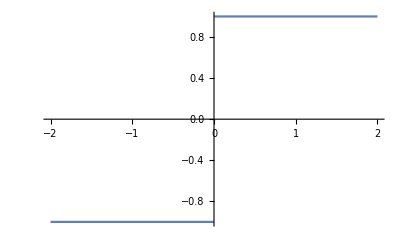

```mathematica
Plot[Sign[x],{x,-2,2}]
```

```mathematica
FullSimplify[Normalize@{1,t}.Normalize@{1,2t},t∈Reals]
```

(1+2 t^2)/(√(1+5 t^2+4 t^4))

```mathematica
FullSimplify[Normalize@{1,1}.Normalize@{1,2t},t∈Reals]
```

(1+2 t)/(√(2+8 t^2))

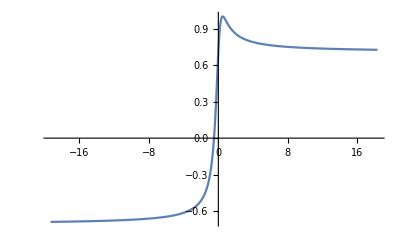

```mathematica
Plot[(1+2 t)/(√(2+8 t^2)),{t,-19.30666666666667,18.30666666666667}]
```

```mathematica
(2 t)/(√(1+4 f''[t]^2)) f'[t]==α √(1+f'[t]^2)
```

(2 t f'[t])/(√(1+4 f''[t]^2))==α √(1+f'[t]^2)

```mathematica
DSolve[(2 t f'[t])/(√(1+4 f''[t]^2))==α √(1+f'[t]^2),{f[t],f[t]},{t}]
```

DSolve[(2 t f'[t])/(√(1+4 f''[t]^2))==α √(1+f'[t]^2),{f[t],f[t]},{t}]

```mathematica
Solve[(2 t f'[t])/(√(1+4 f''[t]^2))==α √(1+f'[t]^2),f''[t]]
```

{{f''[t]→-(√(-α^2+4 t^2 f'[t]^2-α^2 f'[t]^2))/(2 α √(1+f'[t]^2))},{f''[t]→(√(-α^2+4 t^2 f'[t]^2-α^2 f'[t]^2))/(2 α √(1+f'[t]^2))}}

```mathematica
(√(-α^2+4 t^2 f'[t]^2-α^2 f'[t]^2))/(2 α √(1+f'[t]^2))/.α->0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(√(-α^2+4 t^2 f'[t]^2-α^2 f'[t]^2))/(2 α √(1+f'[t]^2))/.α->1
```

(√(-1-f'[t]^2+4 t^2 f'[t]^2))/(2 √(1+f'[t]^2))

```mathematica
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^3
```

(-y'[t] x''[t]+x'[t] y''[t])/((Abs[x'[t]]^2+Abs[y'[t]]^2)^(3/2))

```mathematica
With[{x=Identity},FullSimplify[({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^3,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]]
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
With[{x=Identity},
FullSimplify[({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^3
,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]]
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
With[{x=Identity},
FullSimplify[
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^3
,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]]
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
With[{x=Identity},
FullSimplify[
Norm@{x''[t],y''[t]}.Norm@{x'[t],y'[t]}
,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]]
```

Abs[y''[t]].√(1+y'[t]^2)

```mathematica
FullSimplify[
Norm@{x''[t],y''[t]}.Norm@{x'[t],y'[t]}
,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]
```

√(x''[t]^2+y''[t]^2).√(x'[t]^2+y'[t]^2)

```mathematica
With[{x=Identity},
FullSimplify[
Normalize@{x''[t],y''[t]}.Normalize@{x'[t],y'[t]}
,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]]
```

(Sign[y''[t]] y'[t])/(√(1+y'[t]^2))

```mathematica
FullSimplify[
Normalize@{x''[t],y''[t]}.Normalize@{x'[t],y'[t]}
,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]
```

(x'[t] x''[t]+y'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))

```mathematica
(Sign[y''[t]] y'[t])/(√(1+y'[t]^2))==Sin[t]
```

(Sign[y''[t]] y'[t])/(√(1+y'[t]^2))==Sin[t]

```mathematica
DSolve[(Sign[y''[t]] y'[t])/(√(1+y'[t]^2))==Sin[t],{y[t],y[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[(Sign[y''[t]] y'[t])/(√(1+y'[t]^2))==Sin[t],{y[t],y[t]},{t}]

```mathematica
DSolve[{(Sign[y''[t]] y'[t])/(√(1+y'[t]^2))==Sin[t],y[0]==0},{y[t]},{t}]
```

$Aborted

```mathematica
DSolve[{(a y'[t])/(√(1+y'[t]^2))==Sin[t],y[0]==0},{y[t]},{t}]
```

{{y[t]→Log[√2+√2 √(a^2)]-Log[√2 Cos[t]+√(-1+2 a^2+Cos[2 t])]},{y[t]→-Log[√2+√2 √(a^2)]+Log[√2 Cos[t]+√(-1+2 a^2+Cos[2 t])]}}

```mathematica
Normalize@{t,Sin[t]}.Normalize@{t,Cos[t]}
```

t^2/(√(Abs[t]^2+Abs[Cos[t]]^2) √(Abs[t]^2+Abs[Sin[t]]^2))+(Cos[t] Sin[t])/(√(Abs[t]^2+Abs[Cos[t]]^2) √(Abs[t]^2+Abs[Sin[t]]^2))

```mathematica
FullSimplify[Normalize@{t,Sin[t]}.Normalize@{t,Cos[t]},{t,Sin[t],Cos[t]}∈Reals]
```

(t^2+Cos[t] Sin[t])/(√((t^2+Cos[t]^2) (t^2+Sin[t]^2)))

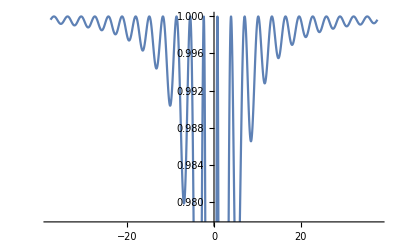

```mathematica
Plot[(t^2+Cos[t] Sin[t])/(√((t^2+Cos[t]^2) (t^2+Sin[t]^2))),{t,-37.69911184307752,37.69911184307752}]
```

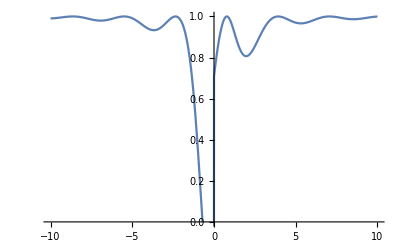

```mathematica
Plot[(t^2+Cos[t] Sin[t])/(√((t^2+Cos[t]^2) (t^2+Sin[t]^2))),{t,-10,10},PlotRange->{0,1}]
```

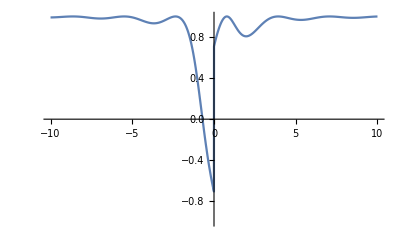

```mathematica
Plot[(t^2+Cos[t] Sin[t])/(√((t^2+Cos[t]^2) (t^2+Sin[t]^2))),{t,-10,10},PlotRange->{-1,1}]
```

```mathematica
3 x^4+-16 x^3+6 x^2+24x+1
```

1+24 x+6 x^2-16 x^3+3 x^4

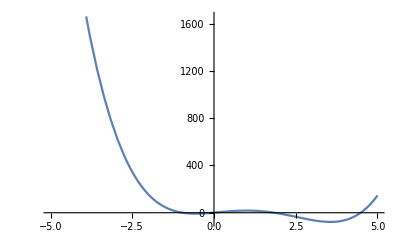

```mathematica
Plot[3 x^4+-16 x^3+6 x^2+24x+1,{x,-5,5}]
```

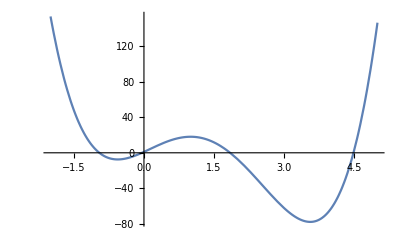

```mathematica
Plot[3 x^4+-16 x^3+6 x^2+24x+1,{x,-2,5}]
```

```mathematica
Manipulate[
Plot[{
Normalize@{0,α}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},
α,
3 x^4+-16 x^3+6 x^2+24x+1
},{x,-2,5}]
,{α,0,1}]
```

```mathematica
Manipulate[
Plot[{
Normalize@{0,α}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},
α,
3 x^4+-16 x^3+6 x^2+24x+1
},{x,-2,5}]
,{α,-4,4}]
```

```mathematica
Manipulate[
Plot[{
Normalize@{0,α}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},
α,
3 x^4+-16 x^3+6 x^2+24x+1
},{x,-2,5}
,PlotRange->{-10,5}]
,{α,-4,4}]
```

```mathematica
Manipulate[
Plot[{
Normalize@{0,α}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},
α,
3 x^4+-16 x^3+6 x^2+24x+1
},{x,-2,5}
,PlotRange->{-50,50}]
,{α,-4,4}]
```

```mathematica
Manipulate[
Plot[{
Normalize@{0,α}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},
α,
3 x^4+-16 x^3+6 x^2+24x+1
},{x,-2,5}
,PlotRange->{-50,50}]
,{α,-50,50}]
```

```mathematica
Manipulate[
Plot[{
Normalize@{x,α}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},
α,
3 x^4+-16 x^3+6 x^2+24x+1
},{x,-2,5}
,PlotRange->{-50,50}]
,{α,-50,50}]
```

```mathematica
Manipulate[
Plot[{
Normalize@{x,α}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},
α,
3 x^4+-16 x^3+6 x^2+24x+1
},{x,-2,5}
,PlotRange->{-1,1}]
,{α,-50,50}]
```

```mathematica
Normalize@{x,0}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1}
```

x^2/(Abs[x] √(Abs[x]^2+Abs[1+24 x+6 x^2-16 x^3+3 x^4]^2))

```mathematica
FullSimplify[Normalize@{x,0}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},x∈Reals]
```

Abs[x]/(√(x^2+(1+x (24+x (6+x (-16+3 x))))^2))

```mathematica
FullSimplify[Normalize@{x,0}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1}==1,x∈Reals]
```

1+x (24+x (6+x (-16+3 x)))==0

```mathematica
Reduce[1+x (24+x (6+x (-16+3 x)))==0]
```

x==Root-0.955Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,1]-0.9554012618124793||x==Root-0.0422Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,2]-0.04216142170022761||x==Root1.84Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,3]1.844510254432838||x==Root4.49Root[1+24 #1+6 #1^2-16 #1^3+3 #1^4&,4]4.486385762413202

```mathematica
FullSimplify[D[Normalize@{x,0}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},x]==D[1,x],x∈Reals]
```

(-1+x^2 (6+x (-32+9 x))) (1+x (24+x (6+x (-16+3 x)))) Sign[x]==0

```mathematica
FullSimplify[D[Normalize@{x,0}.Normalize@{x,3 x^4+-16 x^3+6 x^2+24x+1},{x,2}]==0,x∈Reals]
```

$Aborted

```mathematica
D[1+x (24+x (6+x (-16+3 x))),{x,2}]
```

x (6 x+2 (-16+6 x))+2 (6+x (-16+3 x)+x (-16+6 x))

```mathematica
Solve[x (6 x+2 (-16+6 x))+2 (6+x (-16+3 x)+x (-16+6 x))==0,x]
```

{{x→1/3 (4-√13)},{x→1/3 (4+√13)}}

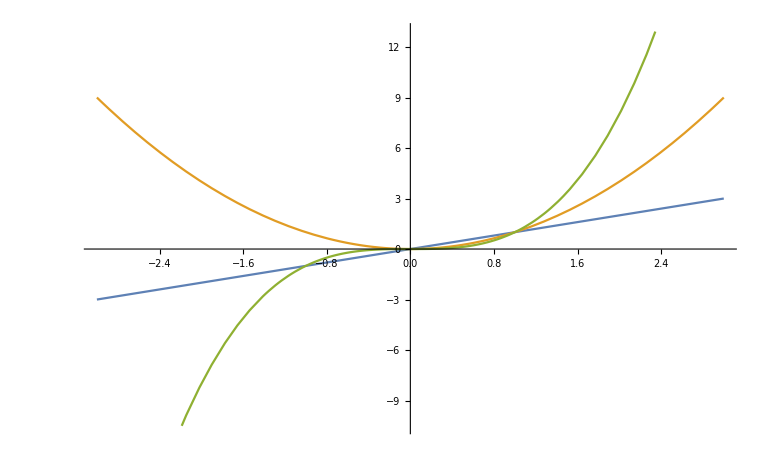

```mathematica
Plot[{x,x x, x x x},{x,-3,3}]
```

```mathematica
Total@{x,x x, x x x}
```

x+x^2+x^3

```mathematica
Normalize@{x,x+x^2+x^3}.Normalize@{x,0}
```

x^2/(Abs[x] √(Abs[x]^2+Abs[x+x^2+x^3]^2))

```mathematica
FullSimplify[Normalize@{x,x+x^2+x^3}.Normalize@{x,0},x∈Reals]
```

1/(√((1+x^2) (2+x (2+x))))

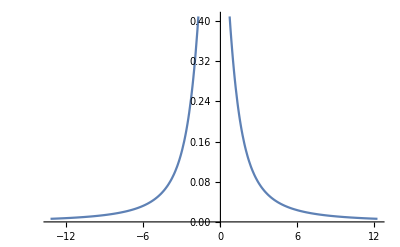

```mathematica
Plot[1/(√((1+x^2) (2+x (2+x)))),{x,-13.239999999999998,12.239999999999998}]
```

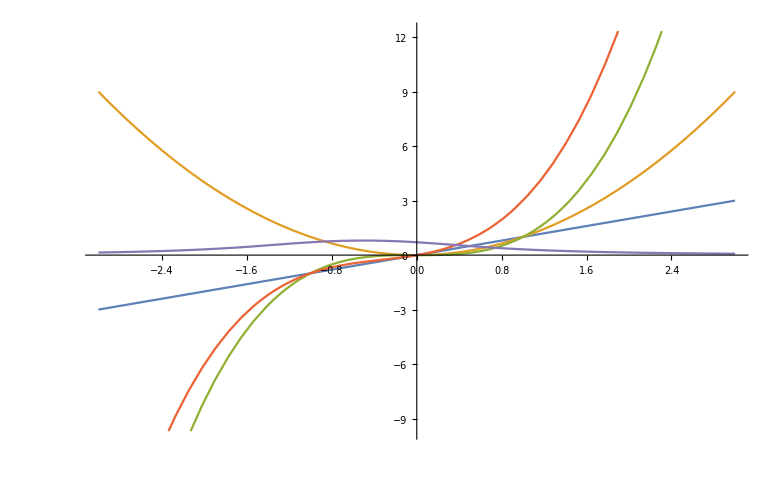

```mathematica
Plot[{x,x x, x x x,x x x+ x x+ x,1/(√((1+x^2) (2+x (2+x))))},{x,-3,3}]
```

```mathematica
Log[x,x]
```

1

```mathematica
Log[x,2]
```

Log[2]/Log[x]

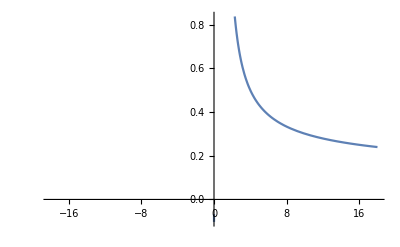

```mathematica
Plot[Log[2]/Log[x],{x,-18.,18.}]
```

```mathematica
D[3 x^4+-16 x^3+6 x^2+24x+1,{x,2}]
```

12-96 x+36 x^2

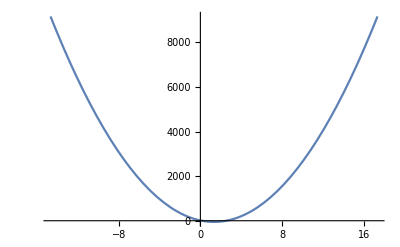

```mathematica
Plot[12-96 x+36 x^2,{x,-14.666666666666666,17.333333333333332}]
```

```mathematica
Normalize@{1,1}.Normalize@D[{x,3 x^4+-16 x^3+6 x^2+24x+1},x]
```

1/(√2 √(1+Abs[24+12 x-48 x^2+12 x^3]^2))+(24+12 x-48 x^2+12 x^3)/(√2 √(1+Abs[24+12 x-48 x^2+12 x^3]^2))

```mathematica
FullSimplify[Normalize@{1,1}.Normalize@D[{x,3 x^4+-16 x^3+6 x^2+24x+1},x],x∈Reals]
```

(25+12 x (1+(-4+x) x))/(√2 √(1+144 (2+x-4 x^2+x^3)^2))

```mathematica
Table[
FullSimplify[Normalize@{1,D[x^i,x]}.Normalize@D[{x,3 x^4+-16 x^3+6 x^2+24x+1},x],x∈Reals]
,{i,1,4,1}]
```

{(25+12 x (1+(-4+x) x))/(√2 √(1+144 (2+x-4 x^2+x^3)^2)),(1+24 x (2+x-4 x^2+x^3))/(√((1+4 x^2) (1+144 (2+x-4 x^2+x^3)^2))),(1+36 x^2 (2+x-4 x^2+x^3))/(√((1+9 x^4) (1+144 (2+x-4 x^2+x^3)^2))),(1+48 x^3 (2+x-4 x^2+x^3))/(√((1+16 x^6) (1+144 (2+x-4 x^2+x^3)^2)))}

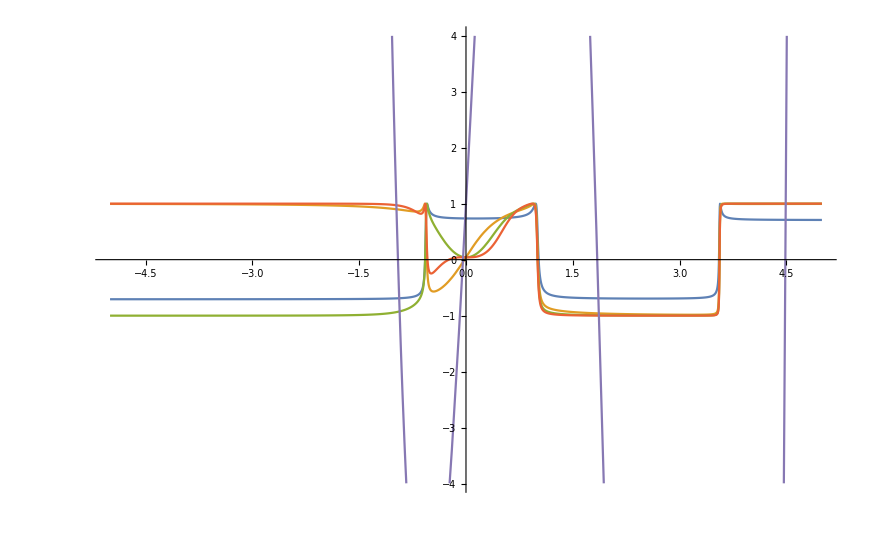

```mathematica
Plot[
{(25+12 x (1+(-4+x) x))/(√2 √(1+144 (2+x-4 x^2+x^3)^2)),(1+24 x (2+x-4 x^2+x^3))/(√((1+4 x^2) (1+144 (2+x-4 x^2+x^3)^2))),(1+36 x^2 (2+x-4 x^2+x^3))/(√((1+9 x^4) (1+144 (2+x-4 x^2+x^3)^2))),(1+48 x^3 (2+x-4 x^2+x^3))/(√((1+16 x^6) (1+144 (2+x-4 x^2+x^3)^2))),3 x^4+-16 x^3+6 x^2+24x+1}
,{x,-5,5}]
```

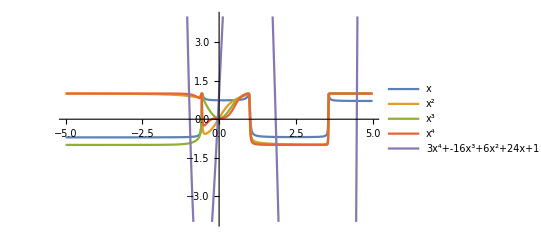

```mathematica
Plot[
{(25+12 x (1+(-4+x) x))/(√2 √(1+144 (2+x-4 x^2+x^3)^2)),(1+24 x (2+x-4 x^2+x^3))/(√((1+4 x^2) (1+144 (2+x-4 x^2+x^3)^2))),(1+36 x^2 (2+x-4 x^2+x^3))/(√((1+9 x^4) (1+144 (2+x-4 x^2+x^3)^2))),(1+48 x^3 (2+x-4 x^2+x^3))/(√((1+16 x^6) (1+144 (2+x-4 x^2+x^3)^2))),3 x^4+-16 x^3+6 x^2+24x+1}
,{x,-5,5}
,PlotLegends->{x,x^2,x^3,x^4,"3x^4+-16x^3+6x^2+24x+1"}]
```

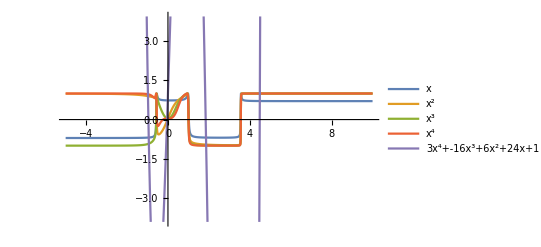

```mathematica
Plot[
{(25+12 x (1+(-4+x) x))/(√2 √(1+144 (2+x-4 x^2+x^3)^2)),(1+24 x (2+x-4 x^2+x^3))/(√((1+4 x^2) (1+144 (2+x-4 x^2+x^3)^2))),(1+36 x^2 (2+x-4 x^2+x^3))/(√((1+9 x^4) (1+144 (2+x-4 x^2+x^3)^2))),(1+48 x^3 (2+x-4 x^2+x^3))/(√((1+16 x^6) (1+144 (2+x-4 x^2+x^3)^2))),3 x^4+-16 x^3+6 x^2+24x+1}
,{x,-5,10}
,PlotLegends->{x,x^2,x^3,x^4,"3x^4+-16x^3+6x^2+24x+1"}]
```

```mathematica
Plot[
{(25+12 x (1+(-4+x) x))/(√2 √(1+144 (2+x-4 x^2+x^3)^2)),(1+24 x (2+x-4 x^2+x^3))/(√((1+4 x^2) (1+144 (2+x-4 x^2+x^3)^2))),(1+36 x^2 (2+x-4 x^2+x^3))/(√((1+9 x^4) (1+144 (2+x-4 x^2+x^3)^2))),(1+48 x^3 (2+x-4 x^2+x^3))/(√((1+16 x^6) (1+144 (2+x-4 x^2+x^3)^2))),3 x^4+-16 x^3+6 x^2+24x+1}
,{x,-5,10}
,PlotLegends->{x,x^2,x^3,x^4,"3x^4+-16x^3+6x^2+24x+1"}]
```

```mathematica
FullSimplify[Normalize@{1,0}.Normalize@D[{x,3 x^4+-16 x^3+6 x^2+24x+1},x],x∈Reals]
```

1/(√(1+144 (2+x-4 x^2+x^3)^2))

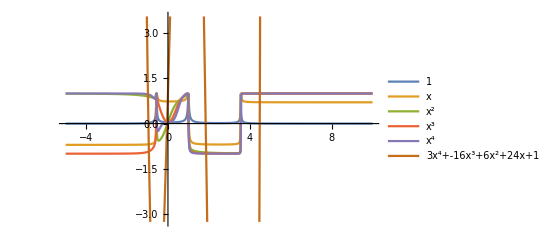

```mathematica
Plot[
{1/(√(1+144 (2+x-4 x^2+x^3)^2)),(25+12 x (1+(-4+x) x))/(√2 √(1+144 (2+x-4 x^2+x^3)^2)),(1+24 x (2+x-4 x^2+x^3))/(√((1+4 x^2) (1+144 (2+x-4 x^2+x^3)^2))),(1+36 x^2 (2+x-4 x^2+x^3))/(√((1+9 x^4) (1+144 (2+x-4 x^2+x^3)^2))),(1+48 x^3 (2+x-4 x^2+x^3))/(√((1+16 x^6) (1+144 (2+x-4 x^2+x^3)^2))),3 x^4+-16 x^3+6 x^2+24x+1}
,{x,-5,10}
,PlotLegends->{1,x,x^2,x^3,x^4,"3x^4+-16x^3+6x^2+24x+1"}]
```

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[f[Dt[x]]]
```

Dt[Dt[x]] f'[Dt[x]]

```mathematica
Dt[Dt[f[x]]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
g[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]]==f[x]
```

g[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]]==f[x]

```mathematica
g[x]=Integrate[x,a]
```

a x

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
ⅇ^(-x^2/2)
```

ⅇ^(-x^2/2)

```mathematica
(1-ⅇ^(-x^2/2))x+(ⅇ^(-x^2/2))(-x)
```

-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x

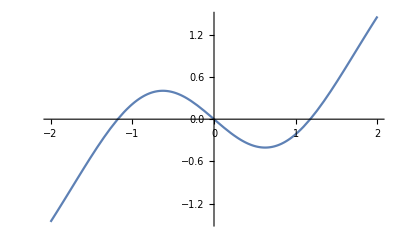

```mathematica
Plot[
-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x
,{x,-2,2}]
```

```mathematica
FullSimplify[
Normalize@{0,D[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x,{x,2}]}.Normalize@{1,D[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x,x]}
,x∈Reals]
```

-((-2+ⅇ^(x^2/2)+2 x^2) Sign[x] Sign[-3+x^2])/(√(2 ⅇ^(x^2)+4 ⅇ^(x^2/2) (-1+x^2)+4 (-1+x^2)^2))

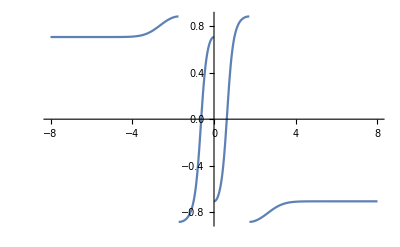

```mathematica
Plot[-((-2+ⅇ^(x^2/2)+2 x^2) Sign[x] Sign[-3+x^2])/(√(2 ⅇ^(x^2)+4 ⅇ^(x^2/2) (-1+x^2)+4 (-1+x^2)^2)),{x,-8,8}]
```

```mathematica
Sign[-3+x^2]
```

Sign[-3+x^2]

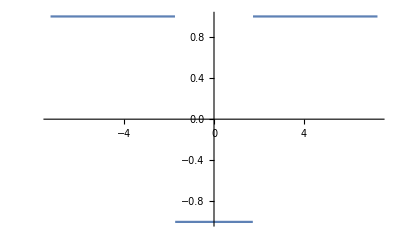

```mathematica
Plot[Sign[-3+x^2],{x,-7.274613391789284,7.274613391789284}]
```

```mathematica
Sign[x] Sign[-3+x^2]
```

Sign[x] Sign[-3+x^2]

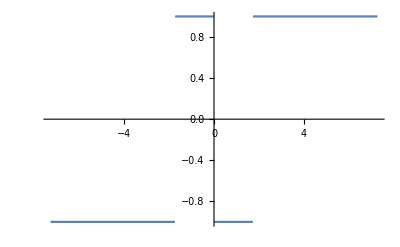

```mathematica
Plot[Sign[x] Sign[-3+x^2],{x,-7.274613391789284,7.274613391789284}]
```

```mathematica
FullSimplify[
Normalize@{0,D[x,{x,2}]}.Normalize@{1,D[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x,x]}
,x∈Reals]
```

0

```mathematica
FullSimplify[
Normalize@{0,D[-x,{x,2}]}.Normalize@{1,D[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x,x]}
,x∈Reals]
```

0

```mathematica
Log[1]
```

0

```mathematica
Sqrt:Integers->Reals
```

Sqrt:ℤ→ℝ

```mathematica
Dt[f[g[x]]]
```

(x Dt[a]+a Dt[x]) f'[a x]

```mathematica
g
```

g

```mathematica
ClearAll[g]
```

```mathematica
Dt[f[g[x]]]
```

Dt[x] f'[g[x]] g'[x]

```mathematica
f[g[x]]/(g[x]/Dt[x])
```

(Dt[x] f[g[x]])/g[x]

```mathematica
Normalize@{1,0}
```

{1,0}

```mathematica
{1,0}
```

```mathematica
Plot[(1-ⅇ^(-x^2/2))x+(ⅇ^(-x^2/2))(-x),{x,-2,2}]
```

-Graphics-

```mathematica
(1-ⅇ^(-x^2/2))+(ⅇ^(-x^2/2))(-1)
```

1-2 ⅇ^(-x^2/2)

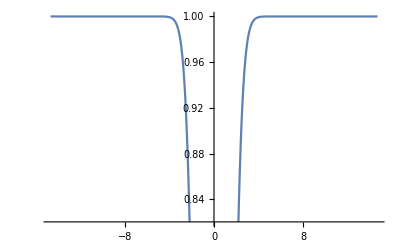

```mathematica
Plot[1-2 ⅇ^(-x^2/2),{x,-14.696938456699069,14.696938456699069}]
```

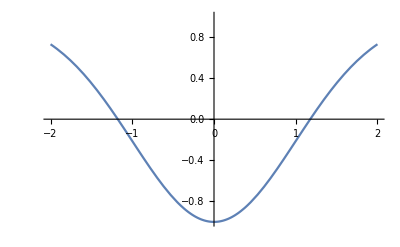

```mathematica
Plot[1-2 ⅇ^(-x^2/2),{x,-2,2},PlotRange->{-1,1}]
```

```mathematica
Integrate[1-2 ⅇ^(-x^2/2),x]
```

x-√(2 π) Erf[x/(√2)]

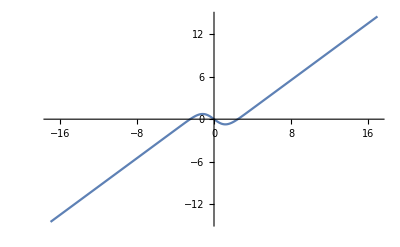

```mathematica
Plot[x-√(2 π) Erf[x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

```mathematica
FullSimplify[{Normalize@{x,x-√(2 π) Erf[x/(√2)]}.Normalize@{x,x},
Normalize@{x,x-√(2 π) Erf[x/(√2)]}.Normalize@{x,-x}}
,x∈Reals]
```

{(x (√2 x-√π Erf[x/(√2)]))/(√(x^2 (x^2+(x-√(2 π) Erf[x/(√2)])^2))),(√π x Erf[x/(√2)])/(Abs[x] √(x^2+(x-√(2 π) Erf[x/(√2)])^2))}

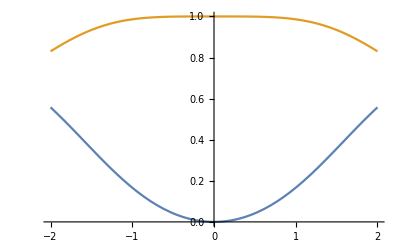

```mathematica
Plot[
{(x (√2 x-√π Erf[x/(√2)]))/(√(x^2 (x^2+(x-√(2 π) Erf[x/(√2)])^2))),(√π x Erf[x/(√2)])/(Abs[x] √(x^2+(x-√(2 π) Erf[x/(√2)])^2))}
,{x,-2,2}]
```

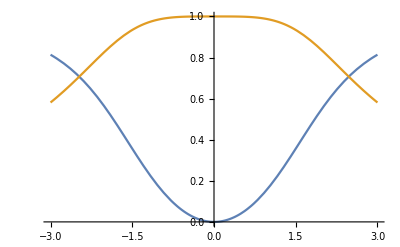

```mathematica
Plot[
{(x (√2 x-√π Erf[x/(√2)]))/(√(x^2 (x^2+(x-√(2 π) Erf[x/(√2)])^2))),(√π x Erf[x/(√2)])/(Abs[x] √(x^2+(x-√(2 π) Erf[x/(√2)])^2))}
,{x,-3,3}]
```

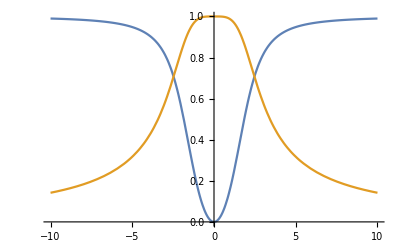

```mathematica
Plot[
{(x (√2 x-√π Erf[x/(√2)]))/(√(x^2 (x^2+(x-√(2 π) Erf[x/(√2)])^2))),(√π x Erf[x/(√2)])/(Abs[x] √(x^2+(x-√(2 π) Erf[x/(√2)])^2))}
,{x,-10,10}]
```